```mathematica
NS["maxNt3_plots2","C:\\Users\\pglpm\\repositories\\maxNt\\scripts\\"];
```

```mathematica
(* maxent distributions at sample level *)
```

```mathematica
<<"ME_homsolution.m";<<"ME_homsolution2.m";
<<"ME_4momsolution.m";
```

```mathematica
(* load first four raw moments from Stensola data (3 ms) *)

n=65;means=Flatten@Import["stensola_norm_binomeans.csv"][[2;;]];
{aa1,aa2,aa3,aa4}=means;
(* find Lagr multipliers, 2 constraints.
MEhomsolution usually give better-precision results than MEhomsolution2 *)
{zj1,zj2,qpop,norm2}=MEhomsolution[aa1,aa2,n,12];
stensolasample2mom=qpop;
Save["stensolasample2mom.m",stensolasample2mom];
```

```mathematica
(* load first four raw moments from Riehle data (3 ms) *)

n=159;means=Flatten@Import["riehle_norm_binomeans.csv"][[2;;]];
{aa1,aa2,aa3,aa4}=means;
(* find Lagr multipliers, 2 constraints.
MEhomsolution usually give better-precision results than MEhomsolution2 *)
{zj1,zj2,qpop,norm2}=MEhomsolution[aa1,aa2,n,12];
riehlesample2mom=qpop;
Save["riehlesample2mom.m",riehlesample2mom];
```

```mathematica
(* load first four raw moments from Stensola data (3 ms) *)

n=65;means=Flatten@Import["stensola_norm_binomeans.csv"][[2;;]];
{aa1,aa2,aa3,aa4}=means;
(* find Lagr multipliers, 2 constraints.
MEhomsolution usually give better-precision results than MEhomsolution2 *)
{zj1,zj2,zj3,zj4,qpop,norm2}=MEhom4moments2[aa1,aa2,aa3,aa4,n,60];
stensolasample4mom=qpop;
Save["stensolasample4mom.m",stensolasample4mom];
```

```mathematica
(* load first four raw moments from Riehle data (3 ms) *)

n=159;means=Flatten@Import["riehle_norm_binomeans.csv"][[2;;]];
{aa1,aa2,aa3,aa4}=means;
(* find Lagr multipliers, 2 constraints.
MEhomsolution usually give better-precision results than MEhomsolution2 *)
{zj1,zj2,zj3,zj4,qpop,norm2}=MEhom4moments2[aa1,aa2,aa3,aa4,n,60];
riehlesample4mom=qpop;
Save["riehlesample4mom.m",riehlesample4mom];
```

```mathematica
(* Plots of maxent distributions for various full-population sizes *)
```

```mathematica
(* stensola *)
which="stensola"; moms=2;
nns=Table[i*1000,{i,10}];
data=Table[
<<(which<>ToString[moms]<>"mom_"<>ToString[nns[[i]]]<>".m");
T@{Range[0,1,1/nns[[i]]],solution[[moms+1]]*nns[[i]]}
,{i,10}];
```

```mathematica
choose={1,2,5,10};plotdata=data[[choose]];
```

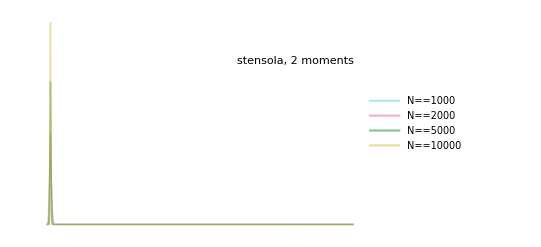

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms],%]
```

stensola2.png

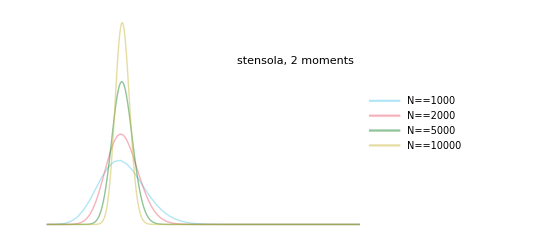

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.05},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_zoom",%]
```

stensola2_zoom.png

```mathematica
Log[10,data[[1,Round[0.5*1000],2]]]
```

-191.97572381

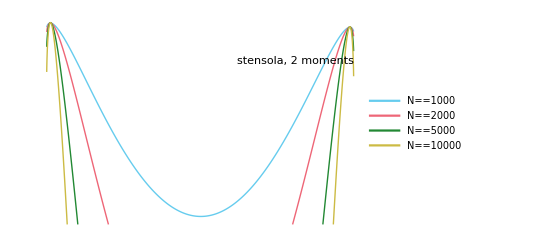

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{All,{10^-200,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_log",%]
```

stensola2_log.png

```mathematica
(* stensola  4 moms*)
which="stensola"; moms=4;
nns=Table[i*1000,{i,10}];
data=Table[
<<(which<>ToString[moms]<>"mom_"<>ToString[nns[[i]]]<>".m");
T@{Range[0,1,1/nns[[i]]],solution[[moms+1]]*nns[[i]]}
,{i,10}];
```

```mathematica
choose={1,2,5,10};plotdata=data[[choose]];
```

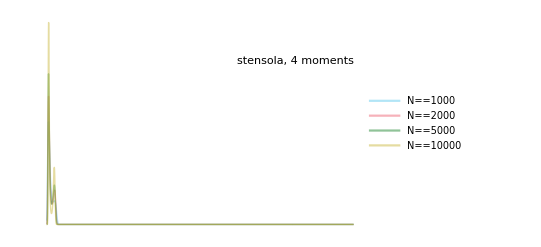

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms],%]
```

stensola4.png

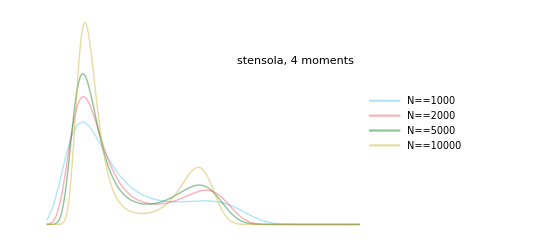

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.05},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_zoom",%]
```

stensola4_zoom.png

```mathematica
Log[10,data[[1,Round[0.06*1000],2]]]
```

-36.12752017

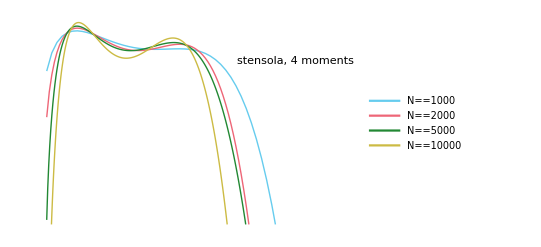

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,0.06},{10^-5,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_log",%]
```

stensola4_log.png

```mathematica
(* riehle 2 moms *)
which="riehle"; moms=2;
nns=Table[i*1000,{i,10}];
data=Table[
<<(which<>ToString[moms]<>"mom_"<>ToString[nns[[i]]]<>".m");
T@{Range[0,1,1/nns[[i]]],solution[[moms+1]]*nns[[i]]}
,{i,10}];
```

```mathematica
choose={1,2,5,10};plotdata=data[[choose]];
```

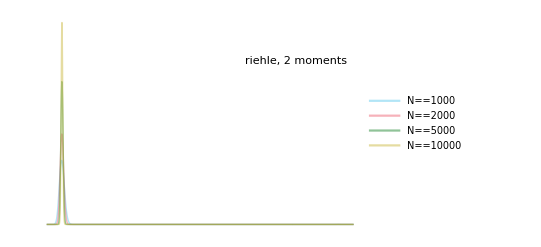

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms],%]
```

riehle2.png

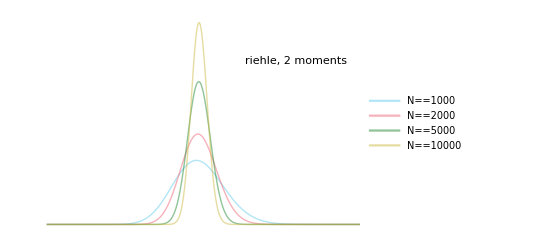

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.1},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_zoom",%]
```

riehle2_zoom.png

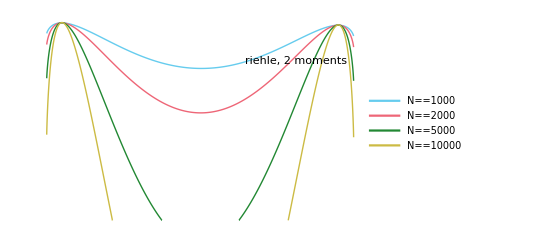

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->Auto,PlotStyle->Directive[solid],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_log",%]
```

riehle2_log.png

```mathematica
(* riehle 4 moms *)
which="riehle"; moms=4;
nns=Table[i*1000,{i,10}];
data=Table[
<<(which<>ToString[moms]<>"mom_"<>ToString[nns[[i]]]<>".m");
T@{Range[0,1,1/nns[[i]]],solution[[moms+1]]*nns[[i]]}
,{i,10}];
```

```mathematica
choose={1,2,5,10};plotdata=data[[choose]];
```

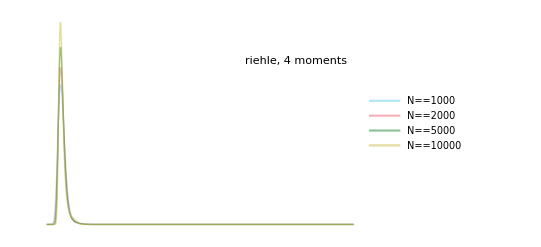

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms],%]
```

riehle4.png

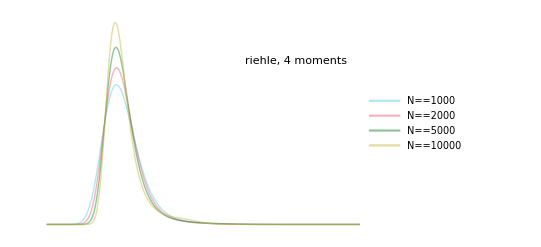

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.2},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_zoom",%]
```

riehle4_zoom.png

```mathematica
Log[10,data[[1,Round[0.25*1000],2]]]
```

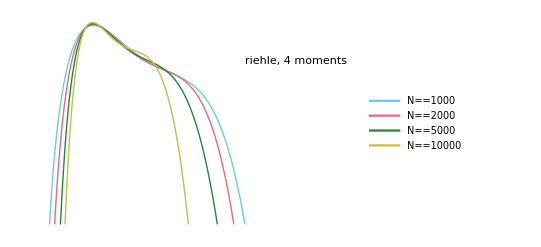

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,0.3},{10^-9,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[N==nns[[i]],{i,choose}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_log",%]
```

riehle4_log.png

```mathematica
(* ***************************************** *)
(* Plots of marginalizations to different sample sizes *)
(* ***************************************** *)
```

```mathematica
(* stensola 2 moms*)
which="stensola"; moms=2;
nns={500,1000,2000};nums=Length@nns;
data=Table[
dist=Flatten@Import[which<>ToString[moms]<>"mom_margto"<>ToString[nns[[i]]]<>".csv"][[2;;]];
T@{Range[0,1,1/nns[[i]]],dist*nns[[i]]}
,{i,nums}];
```

```mathematica
plotdata=data;
```

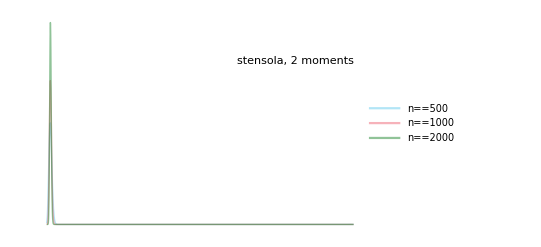

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals",%]
```

stensola2_marginals.png

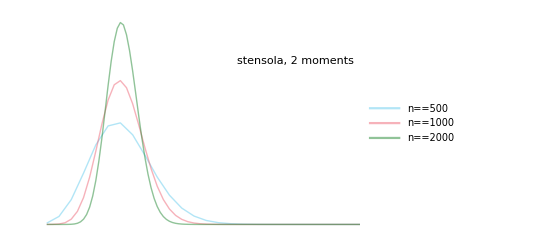

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.05},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_zoom",%]
```

stensola2_marginals_zoom.png

```mathematica
Log[10,data[[3,Round[0.5*1000],2]]]
```

-∞

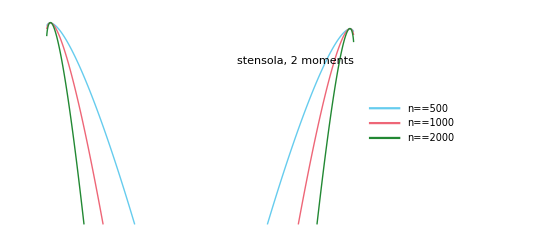

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,All},{10^-140,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_log",%]
```

stensola2_marginals_log.png

```mathematica
(* stensola  4 moms*)
which="stensola"; moms=4;
nns={500,1000,2000};nums=Length@nns;
data=Table[
dist=Flatten@Import[which<>ToString[moms]<>"mom_margto"<>ToString[nns[[i]]]<>".csv"][[2;;]];
T@{Range[0,1,1/nns[[i]]],dist*nns[[i]]}
,{i,nums}];
```

```mathematica
plotdata=data;
```

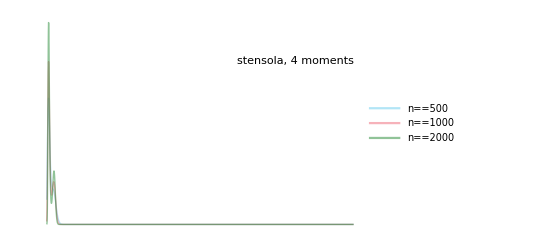

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals",%]
```

stensola4_marginals.png

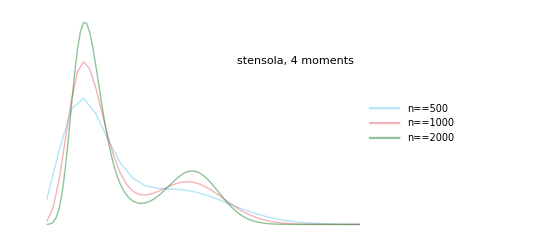

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.05},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_zoom",%]
```

stensola4_marginals_zoom.png

```mathematica
Log[10,data[[3,Round[0.5*1000],2]]]
```

-∞

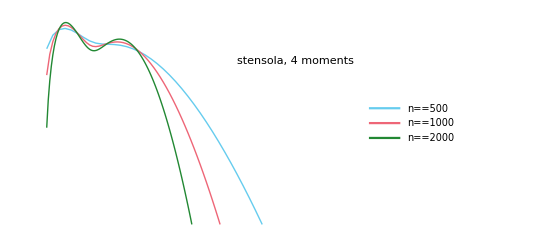

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,0.1},{10^-5,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_log",%]
```

stensola4_marginals_log.png

```mathematica
(* riehle 2 moms *)
which="riehle"; moms=2;
nns={500,1000,2000};nums=Length@nns;
data=Table[
dist=Flatten@Import[which<>ToString[moms]<>"mom_margto"<>ToString[nns[[i]]]<>".csv"][[2;;]];
T@{Range[0,1,1/nns[[i]]],dist*nns[[i]]}
,{i,nums}];
```

```mathematica
plotdata=data;
```

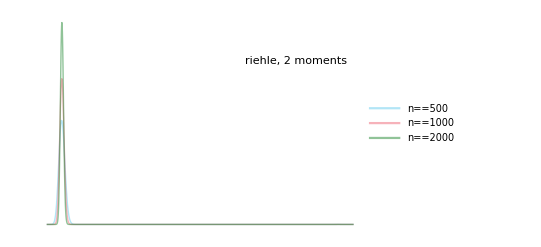

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals",%]
```

riehle2_marginals.png

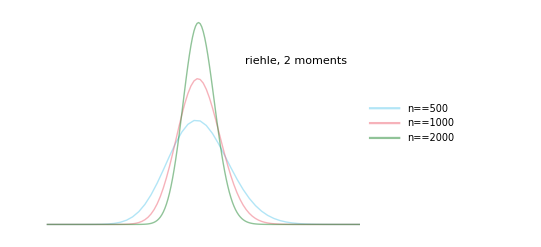

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.1},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_zoom",%]
```

riehle2_marginals_zoom.png

```mathematica
Log[10,data[[3,Round[0.5*1000],2]]]
```

-162.76

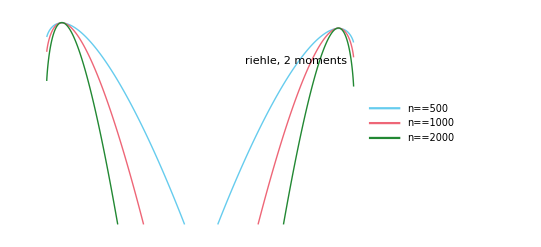

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,All},{10^-140,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_log",%]
```

riehle2_marginals_log.png

```mathematica
(* riehle  4 moms*)
which="riehle"; moms=4;
nns={500,1000,2000};nums=Length@nns;
data=Table[
dist=Flatten@Import[which<>ToString[moms]<>"mom_margto"<>ToString[nns[[i]]]<>".csv"][[2;;]];
T@{Range[0,1,1/nns[[i]]],dist*nns[[i]]}
,{i,nums}];
```

```mathematica
plotdata=data;
```

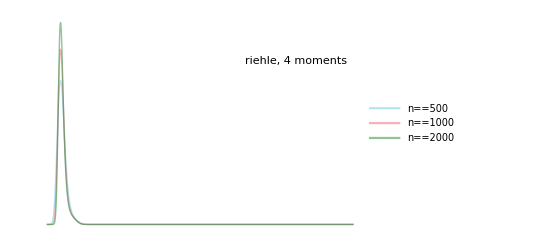

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->All,PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals",%]
```

riehle4_marginals.png

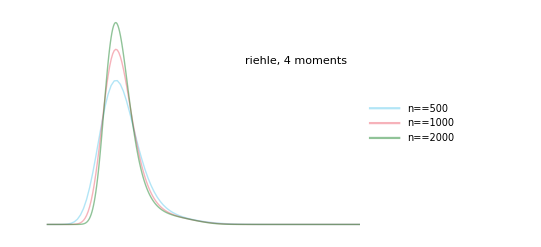

```mathematica
ListPlot[plotdata,Joined->True,PlotRange->{{All,0.2},All},PlotStyle->Directive[solid,Opacity[0.5]],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_zoom",%]
```

riehle4_marginals_zoom.png

```mathematica
Log[10,data[[3,Round[0.5*1000],2]]]
```

-∞

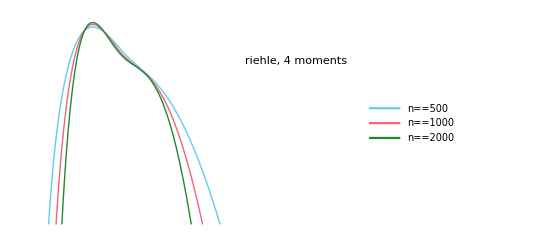

```mathematica
ListLogPlot[plotdata,Joined->True,PlotRange->{{All,0.3},{10^-5,All}},PlotStyle->Directive[solid],PlotLegends->Placed[
Table[n==nns[[i]],{i,nums}],Scaled[{0.5,0.8}]],Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.8,0.8}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"_marginals_log",%]
```

riehle4_marginals_log.png

```mathematica
(* plots of marginalization from different N *)
```

```mathematica
(* maxent distributions at sample level *)
<<"stensolasample2mom";<<"stensolasample4mom";<<"riehlesample2mom";<<"riehlesample4mom";
```

```mathematica
(* stensola *)
which="stensola"; moms=2;
nns={1000,2000,5000,7000,10000};
nx=65;rgn=Range[0,nx];

data=Table[
Flatten@Import[which<>ToString[moms]<>"mom_marg_from"<>ToString[i]<>"to"<>ToString[nx]<>".csv"][[2;;]]
,{i,nns}];
data=Prepend[data,stensolasample2mom];
```

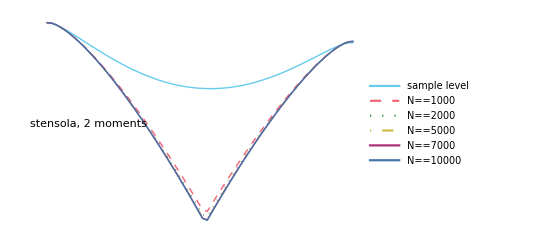

```mathematica
ListLogPlot[data,Joined->True,DataRange->{0,nx},PlotRange->{All,{Auto,All}},PlotStyle->Auto(*Table[{solid,blue,GrayLevel[1-i/10000]},{i,nns}]*),PlotLegends->Placed[
Prepend["sample level"]@Table[N==i,{i,nns}],Scaled[{0.15,0.2}]],FrameLabel->{s,"p"},Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.15,0.5}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"mom_Nmargto"<>ToString@nx<>"_log",%]
```

stensola2mom_Nmargto65_log.png

```mathematica
(* riehle *)
which="riehle"; moms=2;
nns={1000,2000,5000,7000,10000};
nx=159;rgn=Range[0,nx];

data=Table[
Flatten@Import[which<>ToString[moms]<>"mom_marg_from"<>ToString[i]<>"to"<>ToString[nx]<>".csv"][[2;;]]
,{i,nns}];
data=Prepend[data,riehlesample2mom];
```

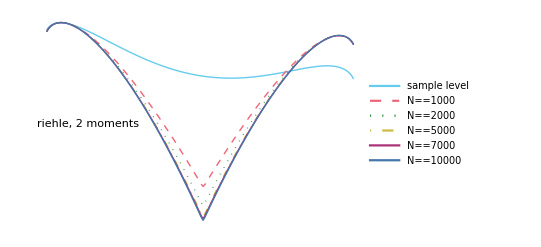

```mathematica
ListLogPlot[data,Joined->True,DataRange->{0,nx},PlotRange->{All,{Auto,All}},PlotStyle->Auto(*Table[{solid,blue,GrayLevel[1-i/10000]},{i,nns}]*),PlotLegends->Placed[
Prepend["sample level"]@Table[N==i,{i,nns}],Scaled[{0.15,0.2}]],FrameLabel->{s,"p"},Epilog->Text[which<>", "<>ToString[moms]<>" moments",Scaled[{0.15,0.5}]]
]
```

```mathematica
expng[which<>ToString[moms]<>"mom_Nmargto"<>ToString@nx<>"_log",%]
```

riehle2mom_Nmargto159_log.png